```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.5,
RandomReal[], (* Prob to buy tool *)
RandomReal[], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&nPTools<=maxPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3,4]
```

{{0,0,1,5,-10},7}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]],a4=agent[[4]],a5=agent[[5]]},
{p,MutateValue[pb],MutateValue[pd],a4,a5}
];
```

0.275068

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=poolHealth/fullToolHealth;
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,800,200];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/4];
newAgents=Join[newAgents,newAgents,newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.1,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,800,200];
history=Append[history, ph];
{ag, history}
];
```

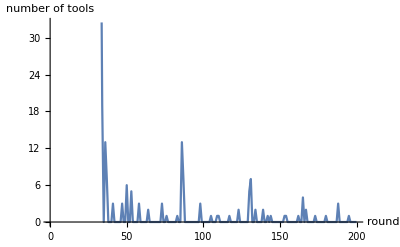

170.86

{{0.5,0,0.0725338,0,300},{0.5,0,0.0725338,0,264},{0.5,0,0.0725338,0,264},{0.5,0,0.0725338,0,261},{0.5,0.0112749,0.0745417,0,253},{0.5,0,0.0725338,0,249},{0.5,0,0.0725338,0,248},{0.5,0,0.0725338,0,245},{0.5,0,0.0725338,0,244},{0.5,0,0.0725338,0,240},{0.5,0,0.0725338,0,240},{0.5,0,0.0725338,0,232},{0.5,0,0.0725338,0,231},{0.5,0,0.0725338,0,227},{0.5,0,0.0725338,0,226},{0.5,0,0.0725338,0,226},{0.5,0,0.0725338,0,223},{0.5,0,0.0725338,0,223},{0.5,0,0.0725338,0,221},{0.5,0,0.0725338,0,220},{0.5,0,0.0725338,0,219},{0.5,0,0.0725338,0,216},{0.5,0,0.0725338,0,215},{0.5,0,0.0725338,0,210},{0.5,0,0,0,209},{0.5,0,0.0725338,0,208},{0.5,0,0.0725338,0,207},{0.5,0,0.0725338,0,207},{0.5,0,0.0725338,0,206},{0.5,0,0.0725338,0,204},{0.5,0,0.0725338,0,203},{0.5,0,0.0725338,0,203},{0.5,0,0.0725338,0,201},{0.5,0,0.0547388,0,200},{0.5,0,0.0725338,0,200},{0.5,0,0.0725338,0,200},{0.5,0,0.0547388,0,198},{0.5,0,0.0725338,0,196},{0.5,0,0.0725338,0,195},{0.5,0,0,0,194},{0.5,0,0.0725338,0,193},{0.5,0,0.0725338,0,193},{0.5,0,0.0725338,0,192},{0.5,0,0,0,190},{0.5,0,0.0547388,0,189},{0.5,0,0.0725338,0,188},{0.5,0,0.0725338,0,187},{0.5,0,0.0725338,0,185},{0.5,0,0.0725338,0,183},{0.5,0,0.0725338,0,181},{0.5,0,0.0725338,0,179},{0.5,0,0.0725338,0,173},{0.5,0,0.0725338,0,173},{0.5,0,0,0,172},{0.5,0,0.0725338,0,172},{0.5,0,0,0,171},{0.5,0,0,0,169},{0.5,0,0.0725338,0,168},{0.5,0,0.0371924,0,167},{0.5,0,0.0547388,0,167},{0.5,0,0.0547388,0,164},{0.5,0,0.0725338,0,161},{0.5,0,0.0725338,0,158},{0.5,0,0.0725338,0,158},{0.5,0,0,0,156},{0.5,0,0.0547388,0,156},{0.5,0,0,0,155},{0.5,0,0.0725338,0,152},{0.5,0,0.0725338,0,150},{0.5,0,0.0725338,0,147},{0.5,0,0,0,146},{0.5,0,0.0725338,0,146},{0.5,0,0.0725338,0,144},{0.5,0,0.0725338,0,141},{0.5,0,0.0725338,0,138},{0.5,0,0,0,137},{0.5,0,0.0547388,0,136},{0.5,0,0.0725338,0,133},{0.5,0,0.0725338,0,132},{0.5,0,0.0725338,0,132},{0.5,0,0,0,129},{0.5,0,0.0725338,0,129},{0.5,0,0.145187,0,129},{0.5,0,0.0725338,0,128},{0.5,0,0.0725338,0,124},{0.5,0,0.0725338,0,121},{0.5,0,0.0725338,0,119},{0.5,0,0.0725338,0,117},{0.5,0.0531888,0.042796,3,116},{0.5,0,0,0,115},{0.5,0,0.0725338,0,110},{0.5,0,0.0725338,0,109},{0.5,0,0.0725338,0,107},{0.5,0,0,0,104},{0.5,0,0.0593494,0,77},{0.5,0,0.178996,0,62},{0.5,0.0574112,0.13247,0,38},{0.5,0.0240393,0.21723,0,22},{0.5,0,0.25629,0,-105},{0.5,0.0924436,0.330234,3,-127}}

```mathematica
{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]],AxesLabel->{"round", "number of tools"}]
N[Total[Map[Function[x,Last[x]],a]]/Length[a]] (*average payoff*)
Sort[a,Last[#1]>Last[#2]&]
```

We see that we get a mixed stable equilibrium where everyone doesn’t donate that much. Below we plot the evolution of pool health over the generations.

```mathematica
hh={};
For[i=1,i≤Length[h],i++,
For[j=1,j≤Length[h[[i]]],j++,
hh=Append[hh,{i,j,h[[i]][[j]]}];
]
];
ListPlot3D[hh]
```

-Graphics3D-

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},avgPHist={},poolHealth=initHealth},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
{ag, history,avgPHist}
];
```

Run the model with 80 initial tools. We see a drop off after 300 rounds. This is probably because some agents realize that they can defect and be better of than anyone else. Or that they realize that they don’t have to buy tools and can just use the pool. Meaning that the tool is used efficiently all the time. We also plot the average payoff for each round.

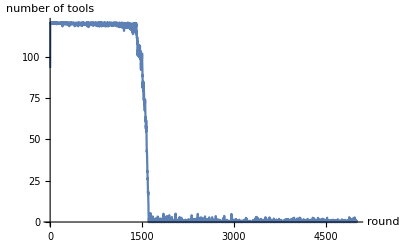

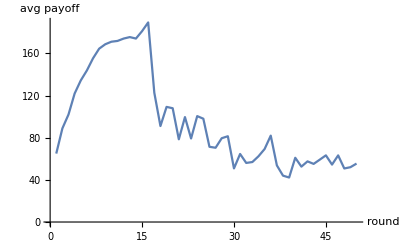

{{0.5,0,0.0750956,0,120},{0.5,0,0.0589259,0,117},{0.5,0,0.0663418,0,112},{0.5,0,0.0750956,0,108},{0.5,0,0.0589259,0,105},{0.5,0,0.0750956,0,104},{0.5,0,0.0750956,0,102},{0.5,0,0.0589259,0,96},{0.5,0,0.0663418,0,90},{0.5,0,0.0750956,0,90},{0.5,0,0.0663418,0,88},{0.5,0,0.0750956,0,88},{0.5,0,0.0750956,0,86},{0.5,0,0.0750956,0,85},{0.5,0,0.0750956,0,85},{0.5,0,0.0750956,0,82},{0.5,0,0.0262045,0,81},{0.5,0,0.0663418,0,81},{0.5,0,0.0750956,0,81},{0.5,0,0.0750956,0,81},{0.5,0,0.0589259,0,80},{0.5,0,0.0750956,0,80},{0.5,0,0.0750956,0,80},{0.5,0,0.0750956,0,79},{0.5,0,0.0750956,0,79},{0.5,0,0.0750956,0,78},{0.5,0,0.0750956,0,78},{0.5,0,0.0663418,0,77},{0.5,0,0.0589259,0,76},{0.5,0,0.0663418,0,76},{0.5,0,0.0750956,0,76},{0.5,0,0.0750956,0,76},{0.5,0,0.0663418,0,75},{0.5,0,0.0750956,0,75},{0.5,0,0.0589259,0,72},{0.5,0,0.0750956,0,71},{0.5,0,0.0750956,0,71},{0.5,0,0.0750956,0,70},{0.5,0,0.0750956,0,69},{0.5,0,0.0750956,0,69},{0.5,0,0.0589259,0,68},{0.5,0,0.0663418,0,68},{0.5,0,0.0750956,0,65},{0.5,0,0.0750956,0,64},{0.5,0,0.0750956,0,63},{0.5,0,0.0750956,0,61},{0.5,0,0.0750956,0,59},{0.5,0,0.0589259,0,57},{0.5,0,0.0589259,0,56},{0.5,0,0.0750956,0,56},{0.5,0,0.0750956,0,55},{0.5,0,0.0750956,0,54},{0.5,0,0.0663418,0,53},{0.5,0,0.0750956,0,53},{0.5,0,0.0750956,0,53},{0.5,0,0.0589259,0,51},{0.5,0,0.0589259,0,51},{0.5,0,0.0589259,0,51},{0.5,0,0.0663418,0,51},{0.5,0,0.0750956,0,51},{0.5,0,0.0750956,0,48},{0.5,0,0.0750956,0,47},{0.5,0,0.0750956,0,46},{0.5,0,0.0750956,0,45},{0.5,0,0.0750956,0,45},{0.5,0,0.0750956,0,44},{0.5,0,0.0663418,0,43},{0.5,0,0.0750956,0,43},{0.5,0,0.0663418,0,42},{0.5,0,0.0589259,0,39},{0.5,0,0.0262045,0,37},{0.5,0,0.0262045,0,36},{0.5,0,0.0589259,0,35},{0.5,0,0.0750956,0,35},{0.5,0,0.0589259,0,34},{0.5,0,0.0750956,0,32},{0.5,0,0.0262045,0,31},{0.5,0,0.0663418,0,30},{0.5,0,0.0750956,0,30},{0.5,0.00998603,0.041563,0,29},{0.5,0,0.0750956,0,29},{0.5,0,0.0750956,0,28},{0.5,0,0.0589259,0,27},{0.5,0,0.0750956,0,27},{0.5,0,0.0750956,0,27},{0.5,0,0.0750956,0,27},{0.5,0,0.0750956,0,26},{0.5,0,0.0750956,0,22},{0.5,0,0.0750956,0,21},{0.5,0,0.0750956,0,21},{0.5,0,0.0589259,0,18},{0.5,0,0.0750956,0,17},{0.5,0,0.0663418,0,9},{0.5,0,0.0589259,0,6},{0.5,0,0.0589259,0,-3},{0.5,0,0.0750956,0,-5},{0.5,0,0.0750956,0,-9},{0.5,0,0.0589259,0,-13},{0.5,0,0.0750956,0,-14},{0.5,0,0.0750956,0,-16}}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,800];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"round", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
```

We try the same thing but with different amount of tools initially.As we can see this doesn’t change the outcome that much. A mixed strategy equilibrium can be observed here as well.

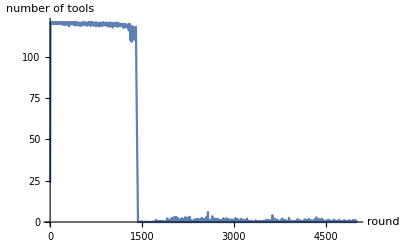

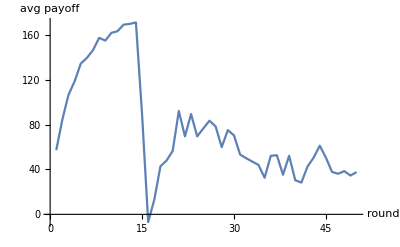

{{0.5,0,0.0670342,0,111},{0.5,0,0.0670342,0,105},{0.5,0,0.0670342,0,92},{0.5,0,0.0670342,0,87},{0.5,0,0.0460956,0,86},{0.5,0,0.0670342,0,86},{0.5,0,0.0670342,0,84},{0.5,0,0.0670342,0,80},{0.5,0,0.0425368,0,76},{0.5,0,0.0670342,0,76},{0.5,0,0.0670342,0,74},{0.5,0,0.0670342,0,74},{0.5,0,0.053504,0,72},{0.5,0,0.0670342,0,72},{0.5,0,0.0425368,0,68},{0.5,0,0.0425368,0,66},{0.5,0,0.0425368,0,65},{0.5,0,0.0670342,0,65},{0.5,0,0.0670342,0,65},{0.5,0,0.0670342,0,65},{0.5,0,0,0,64},{0.5,0,0.0425368,0,62},{0.5,0.177007,0,0,60},{0.5,0,0.0670342,0,60},{0.5,0,0.0670342,0,59},{0.5,0,0.0425368,0,58},{0.5,0,0.0670342,0,57},{0.5,0,0.0425368,0,56},{0.5,0,0.0670342,0,55},{0.5,0,0.0670342,0,55},{0.5,0,0.0425368,0,53},{0.5,0.136202,0,2,52},{0.5,0,0.0670342,0,52},{0.5,0,0.0670342,0,52},{0.5,0.0499735,0.0306783,0,50},{0.5,0.00722588,0.0251478,0,49},{0.5,0.0548061,0.0311913,0,49},{0.5,0,0.0425368,0,48},{0.5,0,0.0670342,0,48},{0.5,0.0548061,0.0311913,0,47},{0.5,0,0.0425368,0,47},{0.5,0,0.0670342,0,47},{0.5,0.0660767,0.0358807,0,45},{0.5,0,0.0460956,0,45},{0.5,0.0118752,0.0662835,0,45},{0.5,0,0.0670342,0,44},{0.5,0,0.0460956,0,43},{0.5,0.177007,0,5,42},{0.5,0.0548061,0.0311913,0,42},{0.5,0.0660767,0.0358807,5,41},{0.5,0,0,0,40},{0.5,0.0481133,0,0,39},{0.5,0,0.0655877,0,38},{0.5,0,0.0425368,0,37},{0.5,0,0.0425368,0,37},{0.5,0,0.0425368,0,37},{0.5,0,0.053504,0,37},{0.5,0,0.0425368,0,36},{0.5,0,0.0670342,0,36},{0.5,0.00722588,0.0251478,0,34},{0.5,0.0660767,0.0358807,4,34},{0.5,0,0.0425368,0,31},{0.5,0,0.0670342,0,31},{0.5,0,0.0670342,0,30},{0.5,0,0.0670342,0,30},{0.5,0,0.0425368,0,28},{0.5,0,0.0425368,0,27},{0.5,0.00574933,0.129389,0,26},{0.5,0.0481133,0,10,25},{0.5,0,0.00735828,0,25},{0.5,0.0660767,0.0358807,0,24},{0.5,0,0.0460956,0,24},{0.5,0.0178689,0.0186259,0,23},{0.5,0,0.0670342,0,22},{0.5,0.0548061,0.0311913,2,21},{0.5,0,0.0425368,0,19},{0.5,0,0.0425368,0,19},{0.5,0.0739562,0,0,18},{0.5,0,0.0655877,0,18},{0.5,0,0.0670342,0,17},{0.5,0.0660767,0.0358807,0,15},{0.5,0,0.0425368,0,15},{0.5,0,0.0670342,0,15},{0.5,0,0.0425368,0,13},{0.5,0.136202,0,10,12},{0.5,0.0178689,0.0186259,0,7},{0.5,0,0.0670342,0,5},{0.5,0,0.0670342,0,3},{0.5,0,0.0425368,0,1},{0.5,0.00722588,0.0251478,1,0},{0.5,0,0.0670342,0,0},{0.5,0.0660767,0.0358807,1,-1},{0.5,0.0660767,0.0358807,4,-4},{0.5,0.0499735,0.0306783,10,-5},{0.5,0,0.053504,0,-5},{0.5,0,0.0425368,0,-18},{0.5,0,0.0670342,0,-18},{0.5,0.0660083,0.115906,0,-32},{0.5,0,0.0670342,0,-44},{0.5,0.124496,0.219703,6,-153}}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,100];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"round", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
```